```mathematica
AoA={-0.15, -0.12,-0.087,0.087,0.12,0.15};
```

```mathematica
DecimalForm[AoA,{2,2}]
```

{-0.15,-0.12,-0.09,0.09,0.12,0.15}

```mathematica
points=ToExpression[Import["/home/tatjam/code/tfg/workdir/geom.dat","String"]];
```

```mathematica
Graphics3D[Polygon[points]]
```

-Graphics3D-

```mathematica
params=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/params_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"]&,AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/params_-0.20_.dat not found during Import.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/params_-0.10_.dat not found during Import.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/params_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
liftOverCamber=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"][[1]]&,AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_-0.20_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_-0.10_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
dragOverCamber=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_drag_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"][[1]]&,AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_drag_-0.20_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_drag_-0.10_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_drag_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
clOverCamberPrandtl=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"][[1]]&,AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_-0.20_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_-0.10_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
cdOverCamperPrandtl=
Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_drag_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"][[1]]&,AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_drag_-0.20_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_drag_-0.10_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_drag_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
sln=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/sln_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"][[1]]&,AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/sln_-0.20_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/sln_-0.10_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/sln_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
wakeGeom=Map[ToExpression[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/wake_geom_" <> ToString[DecimalForm[#, {2, 2}]] <> "_.dat","String"]]&, AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/wake_geom_-0.20_.dat not found during Import.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/wake_geom_-0.10_.dat not found during Import.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/wake_geom_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
wakesln=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/wake_sln_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"][[1]]&,AoA];
```

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/wake_sln_-0.20_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/wake_sln_-0.10_.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Import::nffil: File /home/tatjam/code/tfg/workdir/steady_rectangle/wake_sln_0.10_.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
maxsol=Map[Max[Abs[#]]&, sln];
```

```mathematica
maxsolwake=Map[Max[Abs[#]]&, wakesln];
```

```mathematica
colorEach[p_,c_,i_]:={FaceForm[ColorData["GrayYellowTones"][Abs[c/maxsol[[i]]]]],Polygon[p]}
```

```mathematica
colorEachWrapper[i_][p_,c_]:=colorEach[p,c,i]
```

```mathematica
colorEachWake[p_,c_,i_]:={FaceForm[ColorData["TemperatureMap"][Abs[c/maxsolwake[[i]]]]],Polygon[p]}
```

```mathematica
colorEachWrapperWake[i_][p_,c_]:=colorEachWake[p,c,i]
```

#### Lifting line theory

#### Comparison

```mathematica
graphics0=Map[Legended[Graphics3D[
ArrayFlatten[{EdgeForm[None],MapThread[colorEachWrapper[#],{points, sln[[#]]}],
MapThread[colorEachWrapperWake[#], {wakeGeom[[#]], wakesln[[#]]}]},1],Lighting->{{"Ambient", White}}],{BarLegend[{"GrayYellowTones",{0,maxsol[[#]]}}],
BarLegend[{"TemperatureMap", {0,maxsolwake[[#]]}}]}]&,Table[n,{n,1,Length[AoA]}]];
```

MapThread::mptd: Object $Failed⟦1⟧ at position {2, 2} in MapThread[colorEachWrapper[1],{{{{-5.,0.,-0.5},{-4.97435,0.,-0.5},{-4.97435,0.,-0.497435},{-5.,0.,-0.497435}},{{-5.,0.,-0.497435},{-4.97435,0.,-0.497435},{-4.97435,0.,-0.489765},{-5.,0.,-0.489765}},«7»,{{-5.,0.,-0.306053},{-4.97435,0.,-0.306053},{-4.97435,0.,-0.264482},{-5.,0.,-0.264482}},«951»},$Failed⟦1⟧}] has only 0 of required 1 dimensions.

MapThread::mptd: Object $Failed at position {2, 1} in MapThread[colorEachWrapperWake[1],{$Failed,$Failed⟦1⟧}] has only 0 of required 1 dimensions.

MapThread::mptd: Object $Failed⟦1⟧ at position {2, 2} in MapThread[colorEachWrapper[2],{{{{-5.,0.,-0.5},{-4.97435,0.,-0.5},{-4.97435,0.,-0.497435},{-5.,0.,-0.497435}},{{-5.,0.,-0.497435},{-4.97435,0.,-0.497435},{-4.97435,0.,-0.489765},{-5.,0.,-0.489765}},«7»,{{-5.,0.,-0.306053},{-4.97435,0.,-0.306053},{-4.97435,0.,-0.264482},{-5.,0.,-0.264482}},«951»},$Failed⟦1⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

```mathematica
graphics=Map[ListLinePlot[{liftOverCamber[[#]],clOverCamberPrandtl[[#]]},
Epilog->{InfiniteLine[{0,AoA[[#]]*2π},{1,0}]},PlotLabel->AoA[[#]],PlotLegends->{"Panels", "Prandtl"}]&,Table[n,{n,1,Length[AoA]}]];
```

```mathematica
graphicsdrag=Map[ListLinePlot[{dragOverCamber[[#]],cdOverCamperPrandtl[[#]]},
Epilog->{InfiniteLine[{0,AoA[[#]]*2π},{1,0}]},PlotLabel->AoA[[#]],PlotLegends->{"Panels", "Prandtl"}]&,Table[n,{n,1,Length[AoA]}]];
```

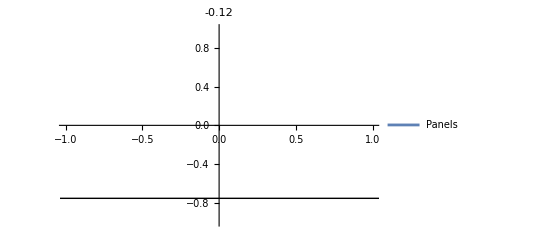

```mathematica
graphics[[2]]
```

```mathematica
graphics0[[2]]
```

-Graphics3D-